Get txt files from wolfram repository.

```mathematica
books=StringJoin@@Get/@ResourceSearch["novels",50];
```

```mathematica
book2=StringJoin@@Get/@Take[ResourceSearch["novels"],{16,20}]
```

3235072
 |  |  |  |

Export to raw data.

```mathematica
Export["Desktop/MMA/project/wikiData/rawData12.txt",books]
```

Desktop/MMA/project/wikiData/rawData12.txt

```mathematica
Export["Desktop/MMA/project/wikiData/rawData13.txt",book2]
```

Desktop/MMA/project/wikiData/rawData13.txt

Import and clean up.

```mathematica
totalData=Join[Normal@trainData[12],Normal@trainData[4],Normal@trainData[5]];
```

```mathematica
Length@totalData
```

63252

```mathematica
order=RandomSample[Range[63252]];
```

```mathematica
trainingSet=totalData[[Take[order,50000]]];
```

```mathematica
validationSet=totalData[[Take[order,{50001,60000}]]];
```

```mathematica
testSet=totalData[[Take[order,{60001,-1}]]];
```

```mathematica
NetTrain[net,trainingSet,All,ValidationSet->validationSet]
```

NetTrainResultsObject[<>]

```mathematica
net["Properties"]
```

{BatchErrorRateList,BatchLossList,BatchSize,CheckpointingFiles,CompactErrorRateEvolutionPlot,CompactLossEvolutionPlot,ErrorRateEvolutionPlot,EvolutionPlots,FinalLearningRate,FinalRoundErrorRate,FinalRoundLoss,FinalValidationErrorRate,FinalValidationLoss,InitialLearningRate,LossEvolutionPlot,LowestValidationErrorRate,LowestValidationLoss,LowestValidationRound,MeanBatchesPerSecond,MeanInputsPerSecond,NetTrainInputForm,OptimizationMethod,RoundErrorRateList,RoundLossList,TotalBatches,TotalInputs,TotalRounds,TotalTrainingTime,TrainedNet,TrainingNet,ValidationErrorRateList,ValidationErrorRateSeries,ValidationLossList,ValidationLossSeries,VersionNumber,WeightsLearningRateMultipliers}

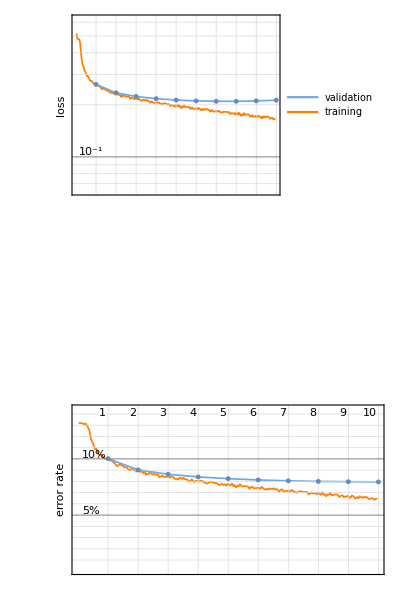

```mathematica
%39["EvolutionPlots"]
```

```mathematica
NetTrain[net6,Normal@trainData[11],All,ValidationSet->Normal@trainData[13]]
```

NetTrainResultsObject[<>]

```mathematica
net=%39
```

NetTrainResultsObject[<>]

```mathematica
DumpSave["net.mx",a]
```

{NetTrainResultsObject[<>]}

colon. Analysis of pauses vs. punctuation.

wikipedia

quotation mark in novels

visualization

```mathematica
Length@testSet
```

3252

```mathematica
(Keys/@Take[testSet,4])[[1]]
```

food discourse to a disciplined level based on his views of french tradition and morals grimod aimed to reestablish order lost after the revolution and institute gastronomy as a serious subject in france grimod expanded gastronomic literature to the three forms of the genre the guidebook the gastronomic treatise and the gourmet periodical the invention of gastronomic literature coincided with important cultural transformations in france that increased the relevance of the subject the end of nobility in france changed how people consumed food fewer wealthy households employed cooks and the new bourgeoisie class wanted to assert their status by consuming elitist food the emergence of the restaurant satisfied these social needs and provided good food available for popular consumption the center of culinary excellence in france shifted from versailles to paris a city with a competitive and innovative culinary culture the culinary commentary of grimod and other gastronomes influenced the tastes and expectations of consumers in an unprecedented manner as a third party to the consumer chef interaction the french origins of gastronomy explain the widespread use of french terminology in gastronomic literature gastronomic literature pascal ory criticizes is conceptually vague relying heavily on anecdotal evidence and using confusing poorly